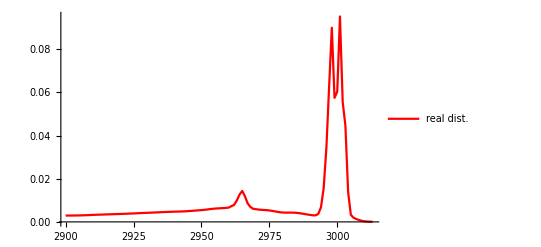

```mathematica
data=Import["/home/petergu/MyHome/USTCcomputer/2019Autumn/CompPhys/HW7/data.TXT","Table"];
data2=Drop[data,1];
data2[[All,2]]/=395418.5;
real=ListLinePlot[data2,PlotRange->All,PlotLegends->{"real dist."},PlotStyle->RGBColor["Red"]]
```

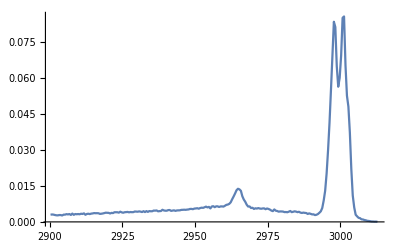

```mathematica
data1=Import["/home/petergu/MyHome/USTCcomputer/2019Autumn/CompPhys/HW7/data1.csv"][[1]];
(*p1=SmoothHistogram[data1,PlotRange->All]*)
p1=HistogramList[data1,{0.5}];
bin=p1[[1]];
Length[bin];
Length[p1[[2]]];
binmid=Range[Length[bin]-1];
For[i=1,i<Length[bin],i++,
binmid[[i]]=(bin[[i]]+bin[[i+1]])/2;
];
(*ListPlot[binmid]*)
Length[binmid];
cnt=p1[[2]]/(Length[data1]*(0.5));
(*p1=ArrayReshape[p1,{Length[p1[[1]]],2}];*)
(*p1[[2,All]]/=Length[data1]*0.2;*)
ListLinePlot[Transpose[{binmid,cnt}],PlotRange->All]
data2=Import["/home/petergu/MyHome/USTCcomputer/2019Autumn/CompPhys/HW7/data2.csv"][[1]];
(*p2=SmoothHistogram[data2,PlotRange->All]*)
(*Show[real,p1,p2]*)
```

```mathematica
Transpose[{{1,2,3,4},{5,6,6,7}}]
```

{{1,5},{2,6},{3,6},{4,7}}